```mathematica
Module[{m=1},
sol=DSolveValue[{y''[x]+m y'[x] + y[x]==0,y[0]==0,y'[0]==1},y,x]
][[2]]

 Module[{m=3},
sol=DSolveValue[{y''[x]+m y'[x] + y[x]==0,y[0]==0,y'[0]==1},y,x]
][[2]]

 Module[{m=4},
sol=DSolveValue[{y''[x]+m y'[x] + y[x]==0,y[0]==0,y'[0]==1},y,x]
][[2]]
```

(2 ⅇ^(-x/2) Sin[(√3 x)/2])/(√3)

-(ⅇ^((-3/2-(√5)/2) x)-ⅇ^((-3/2+(√5)/2) x))/(√5)

-(ⅇ^((-2-√3) x)-ⅇ^((-2+√3) x))/(2 √3)

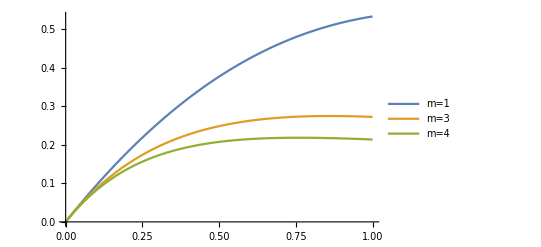

```mathematica
Plot[{(2 ⅇ^(-x/2) Sin[(√3 x)/2])/(√3), -(ⅇ^((-3/2-(√5)/2) x)-ⅇ^((-3/2+(√5)/2) x))/(√5), -(ⅇ^((-2-√3) x)-ⅇ^((-2+√3) x))/(2 √3)},{x,0,1},PlotLegends->{"m=1","m=3","m=4"}]
```

```mathematica
ue=Cos[2 π x]; 
Module[{m=1},
sol=DSolveValue[{y''[x]+y'[x] + y[x] + 3 m ue^2 y[x]==0,y[0]==0,y'[0]==1},y,x]
][[2]]

Module[{m=3},
sol=DSolveValue[{y''[x]+y'[x] + y[x] + 3 m ue^2 y[x]==0,y[0]==0,y'[0]==1},y,x]
][[2]]
```

(ⅇ^(-x/2) MathieuS[9/(16 π^2),-3/(16 π^2),2 π x])/(2 π MathieuSPrime[9/(16 π^2),-3/(16 π^2),0])

(ⅇ^(-x/2) MathieuS[21/(16 π^2),-9/(16 π^2),2 π x])/(2 π MathieuSPrime[21/(16 π^2),-9/(16 π^2),0])

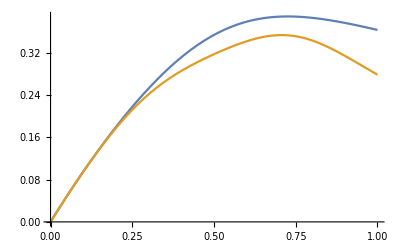

```mathematica
Plot[{N[(ⅇ^(-x/2) MathieuS[9/(4 π^2),3/(4 π^2),π x])/(π MathieuSPrime[9/(4 π^2),3/(4 π^2),0])],N[(ⅇ^(-x/2) MathieuS[15/(16 π^2),3/(8 π^2),2 π x])/(2 π MathieuSPrime[15/(16 π^2),3/(8 π^2),0])]},{x,0,1}]
```